21

{1+(-1+ξ/2) (1+ξ),(1-ξ) (1+ξ),1/2 ξ (1+ξ)}

{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}

{{23.3467,-26.66,3.33},{-26.66,53.3867,-26.66},{3.33,-26.66,23.3467}}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

0

0

0.00333333

0.00333333

0.0633333

0.03

{1,0,0}

{1,0,0}

{0,0,1}

{0,0,1}

{0.,0.00743637,0.0147663,0.0218831,0.0286795,0.0350476,0.0408782,0.0460608,0.0504834,0.0540321,0.0565906,0.0580403,0.0582599,0.0571249,0.0545074,0.0502758,0.0442945,0.0364236,0.0265183,0.0144289,0.}

{}

{0.}

{0.,0.00743637,0.0147663,0.0147663,0.0218831,0.0286795,0.0286795,0.0350476,0.0408782,0.0408782,0.0460608,0.0504834,0.0504834,0.0540321,0.0565906,0.0565906,0.0580403,0.0582599,0.0582599,0.0571249,0.0545074,0.0545074,0.0502758,0.0442945,0.0442945,0.0364236,0.0265183,0.0265183,0.0144289,0.}

{y[x]→-(ⅇ^-x (-ⅇ+ⅇ^(1+2 x)+ⅇ^x x-ⅇ^(2+x) x))/(-1+ⅇ^2)}

-(ⅇ^-x (-ⅇ+ⅇ^(1+2 x)+ⅇ^x x-ⅇ^(2+x) x))/(-1+ⅇ^2)

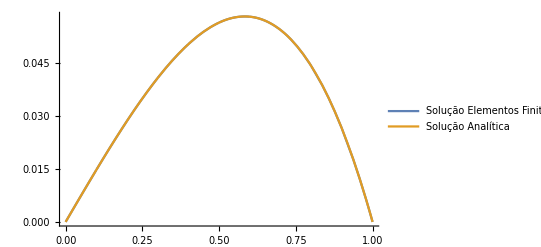

0.00642696

0.115918

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
GaussQ[g_,n_,a_,b_]:=Total[g[First[#]]*Last[#]&/@GaussianQuadratureWeights[n,a,b]]
α=1;γ=1;
u0=0;u1=0;
n=10;h=1/n;np=4;m=n*2+1
f[x_]:=x
φ={InterpolatingPolynomial[{{-1,1},{0,0},{1,0}},ξ],InterpolatingPolynomial[{{-1,0},{0,1},{1,0}},ξ],InterpolatingPolynomial[{{-1,0},{0,0},{1,1}},ξ]}
K={{,,},{,,},{,,}}
K=α*(2/h)*Table[GaussQ[D[φ[[r]],ξ]*D[φ[[s]],ξ]/.ξ->#&,np,-1,1],{r,3},{s,3}]+γ*(h/2)*Table[GaussQ[φ[[r]]*φ[[s]]/.ξ->#&,np,-1,1],{r,3},{s,3}]


F1=ConstantArray[0,{m}]
For[i=1,i<m,i=i+2,

F1[[i;;i+2]]=F1[[i;;i+2]]+(h/2)*Table[GaussQ[((f[x]/.x->(h/2*(i-1)+h/2*(ξ+1)))*φ[[r]])/.ξ->#&,np,-1,1],{r,3}];


]

K1=ConstantArray[0,{m,m}]
For[i=1,i<m-1,i=i+2,
K1[[i;;i+2,i;;i+2]]=K1[[i;;i+2,i;;i+2]]+K;

]
F1[[1]]=u0
F1[[m]]=u1
F1[[2]]=F1[[2]]-K1[[2,1]]*u0
F1[[3]]=F1[[3]]-K1[[3,1]]*u0
F1[[m-1]]=F1[[m-1]]-K1[[m-1,m]]*u1
F1[[m-2]]=F1[[m-2]]-K1[[m-2,m]]*u1
K1[[1,1;;3]]={1,0,0}
K1[[1;;3,1]]={1,0,0}
K1[[m,m-2;;m]]={0,0,1}
K1[[m-2;;m,m]]={0,0,1}

w=LinearSolve[K1,F1]

LagrangeP[p1_]:={Piecewise[{{InterpolatingPolynomial[{{p1,1},{p1+h/2,0},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h/2,1},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h/2,0},{p1+h,1}},x],p1<=x≤p1+h}},0]}

ϕ={}
For[i=1,i<=n,i++,
AppendTo[ϕ,LagrangeP[(i-1)*h][[1]]];
AppendTo[ϕ,LagrangeP[(i-1)*h][[2]]];
AppendTo[ϕ,LagrangeP[(i-1)*h][[3]]]
]

W1={w[[1]]}
For[i=2,i<m,i++,
W1=Join[W1,ConstantArray[w[[i]],{Mod[i,2]+1}]]
]
W1=Join[W1,{w[[m]]}]
Clear[Uh]
Uh[x_]:=W1.ϕ
solution=DSolve[{-α*y''[x]+γ*y[x]==f[x],y[0]==u0,y[1]==u1},y[x],x][[1]]
u[x_]=y[x]/.solution[[1]]
G7=Plot[{Uh[x],u[x]},{x,0,1},PlotRange->All,ImageSize->400,PlotLegends->{"Solução Elementos Finitos","Solução Analítica"},AxesStyle->Black]
G[x_]:=(u[x]-Uh[x])^2
(Sum[h/2*Sum[GaussianQuadratureWeights[4,-1,1][[l]][[2]]*(G[x]/.x->(i*h+h/2*(GaussianQuadratureWeights[4,-1,1][[l]][[1]]+1))),{l,1,4}],{i,0,n}])^(1/2)
G1[x_]:=(D[u[x],x]-D[Uh[x],x])^2
(Sum[h/2*Sum[GaussianQuadratureWeights[4,-1,1][[l]][[2]]*(G1[x]/.x->(i*h+h/2*(GaussianQuadratureWeights[4,-1,1][[l]][[1]]+1))),{l,1,4}],{i,0,n}])^(1/2)
```

```mathematica
Export["1Quadratico_n10.png",G7]
```

1Quadratico_n10.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["1Quadratico_n10.png"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["1Quadratico_n5.png"]]]
```

```mathematica
w//MatrixForm
```

(0.
0.00743637
0.0147663
0.0218831
0.0286795
0.0350476
0.0408782
0.0460608
0.0504834
0.0540321
0.0565906
0.0580403
0.0582599
0.0571249
0.0545074
0.0502758
0.0442945
0.0364236
0.0265183
0.0144289
0.)

```mathematica
({{0.}, {0.014766339096509068}, {0.0286794883941844}, {0.040878298844700234}, {0.05048329847284069}, {0.05659081812299865}, {0.05825980742403746}, {0.05450780977788861}, {0.044294428846233136}, {0.026518991243718575}, {0.}})
```